```mathematica
Clear[κ,λ,μ]
RRR={κ*λ*(1+μ)^2/(1+μ*κ)^2,(κ+μ)^2/(1+μ*κ)^2}
RG[LLL_]:=Together[{κ*λ*(1+μ)^2/(1+μ*κ)^2,(κ+μ)^2/(1+μ*κ)^2}/.κ->LLL[[1]]/.λ->LLL[[2]]]
InitRG={μ^2,1};
L=InitRG
```

{(κ λ (1+μ)^2)/(1+κ μ)^2,(κ+μ)^2/(1+κ μ)^2}

{μ^2,1}

```mathematica
μ=N[301/100,1000];
L=InitRG;
For[i=1,i<10,i++,Print[i,"   ",N[L=RG[L]]]]
Clear[L,μ]
```

1   {0.182281,0.182281}

2   {0.22277,4.24899}

3   {5.45405,3.74487}

4   {1.08271,0.23617}

5   {0.226683,0.923452}

6   {1.18934,3.70156}

7   {3.37493,0.84071}

8   {0.366425,0.327414}

9   {0.436232,2.57787}

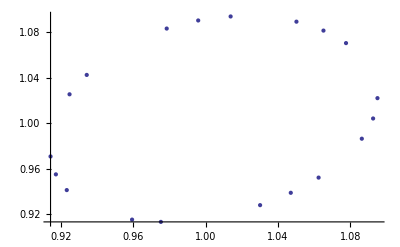

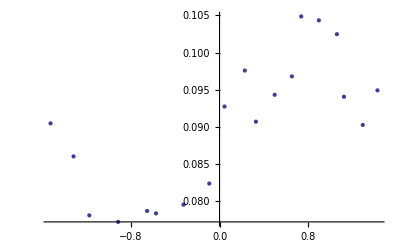

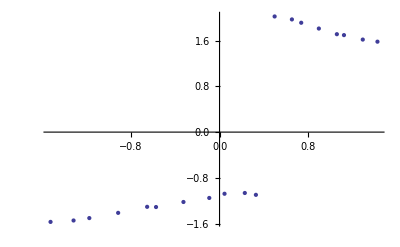

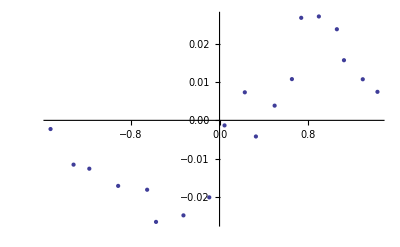

```mathematica
m=3001;
μ=N[m/1000,3000];
L=InitRG;
For[i=1,i<4200,i++,L=RG[L]];
MyList={};
RhoList={};
dPhiList={};
dRhoList={};
For[i=1,i<20,i++,
ϕ=ArcTan[(L[[2]]-1)/(L[[1]]-1)];
ρ=Sqrt[(L[[2]]-1)^2+(L[[1]]-1)^2];
AppendTo[RhoList,N[{ϕ,ρ}]];
OldL=L;
AppendTo[MyList,N[L=RG[L],10]];
Δϕ=ϕ-ArcTan[(L[[2]]-1)/(L[[1]]-1)];
Δρ=ρ-Sqrt[(L[[2]]-1)^2+(L[[1]]-1)^2];
AppendTo[dPhiList,N[{ϕ,Δϕ}]];
AppendTo[dRhoList,N[{ϕ,Δρ}]];
]
P[m]=ListPlot[MyList,Joined->False]
R[m]=ListPlot[RhoList]
dP[m]=ListPlot[dPhiList]
dR[m]=ListPlot[dRhoList]
Clear[L,μ]
```

ArcTan[2]

0.075

0.1

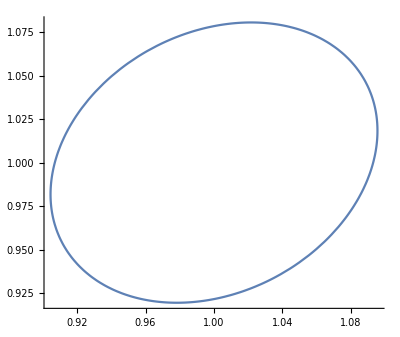

```mathematica
υ=ArcTan[2]
qa=0.075
qb=0.1
Param=ParametricPlot[{1+qa*Cos[ϕ]*Cos[υ]+qb*Sin[ϕ]*Sin[υ],1-qa*Cos[ϕ]*Sin[υ]+qb*Sin[ϕ]*Cos[υ]},{ϕ,0,2Pi}]
```

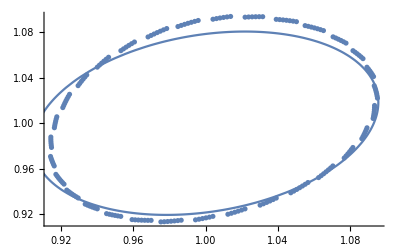

```mathematica
Show[P[3001],Param]
```

```mathematica
Clear[ϕ,ψ,a,b,q]
```

```mathematica
Simplify[{RRR[[1]]-κ,RRR[[2]]-λ}]
```

{κ (-1+(λ (1+μ)^2)/(1+κ μ)^2),-λ+(κ+μ)^2/(1+κ μ)^2}

```mathematica
%/.κ->1+q*a*Cos[ψ]*Cos[ϕ]+q*b*Sin[ψ]Sin[ϕ]/.λ->1+q*a*Sin[ψ]*Cos[ϕ]+q*b*Cos[ψ]Sin[ϕ]/.μ->3+q^2*Δμ
```

{(1+a q Cos[ϕ] Cos[ψ]+b q Sin[ϕ] Sin[ψ]) (-1+((4+q^2 Δμ)^2 (1+b q Cos[ψ] Sin[ϕ]+a q Cos[ϕ] Sin[ψ]))/((1+(3+q^2 Δμ) (1+a q Cos[ϕ] Cos[ψ]+b q Sin[ϕ] Sin[ψ]))^2)),-1-b q Cos[ψ] Sin[ϕ]-a q Cos[ϕ] Sin[ψ]+((4+q^2 Δμ+a q Cos[ϕ] Cos[ψ]+b q Sin[ϕ] Sin[ψ])^2)/((1+(3+q^2 Δμ) (1+a q Cos[ϕ] Cos[ψ]+b q Sin[ϕ] Sin[ψ]))^2)}

```mathematica
Series[%,{q,0,3}]
```

{(-3/2 a Cos[ϕ] Cos[ψ]+b Cos[ψ] Sin[ϕ]+a Cos[ϕ] Sin[ψ]-3/2 b Sin[ϕ] Sin[ψ]) q+1/16 (3 a^2 Cos[ϕ]^2 Cos[ψ]^2-8 a b Cos[ϕ] Cos[ψ]^2 Sin[ϕ]-8 a^2 Cos[ϕ]^2 Cos[ψ] Sin[ψ]+6 a b Cos[ϕ] Cos[ψ] Sin[ϕ] Sin[ψ]-8 b^2 Cos[ψ] Sin[ϕ]^2 Sin[ψ]-8 a b Cos[ϕ] Sin[ϕ] Sin[ψ]^2+3 b^2 Sin[ϕ]^2 Sin[ψ]^2) q^2+1/16 (-2 a Δμ Cos[ϕ] Cos[ψ]+3 a^2 b Cos[ϕ]^2 Cos[ψ]^3 Sin[ϕ]+3 a^3 Cos[ϕ]^3 Cos[ψ]^2 Sin[ψ]-2 b Δμ Sin[ϕ] Sin[ψ]+6 a b^2 Cos[ϕ] Cos[ψ]^2 Sin[ϕ]^2 Sin[ψ]+6 a^2 b Cos[ϕ]^2 Cos[ψ] Sin[ϕ] Sin[ψ]^2+3 b^3 Cos[ψ] Sin[ϕ]^3 Sin[ψ]^2+3 a b^2 Cos[ϕ] Sin[ϕ]^2 Sin[ψ]^3) q^3+O[q]^4,(-a Cos[ϕ] Cos[ψ]-b Cos[ψ] Sin[ϕ]-a Cos[ϕ] Sin[ψ]-b Sin[ϕ] Sin[ψ]) q+(a^2 Cos[ϕ]^2 Cos[ψ]^2+2 a b Cos[ϕ] Cos[ψ] Sin[ϕ] Sin[ψ]+b^2 Sin[ϕ]^2 Sin[ψ]^2) q^2+1/16 (-4 a Δμ Cos[ϕ] Cos[ψ]-15 a^3 Cos[ϕ]^3 Cos[ψ]^3-4 b Δμ Sin[ϕ] Sin[ψ]-45 a^2 b Cos[ϕ]^2 Cos[ψ]^2 Sin[ϕ] Sin[ψ]-45 a b^2 Cos[ϕ] Cos[ψ] Sin[ϕ]^2 Sin[ψ]^2-15 b^3 Sin[ϕ]^3 Sin[ψ]^3) q^3+O[q]^4}

```mathematica
Coefficient[%,q,1]
```

{1/2 (-a Cos[ϕ] Cos[ψ]+2 b Cos[ψ] Sin[ϕ]-2 a Cos[ϕ] Sin[ψ]-b Sin[ϕ] Sin[ψ]),-a Cos[ϕ] Cos[ψ]-b Sin[ϕ] Sin[ψ]}

```mathematica
Collect[%,{Cos[ϕ],Sin[ϕ]},Factor]
```

{1/2 b Sin[ϕ] (2 Cos[ψ]-Sin[ψ])-1/2 a Cos[ϕ] (Cos[ψ]+2 Sin[ψ]),-a Cos[ϕ] Cos[ψ]-b Sin[ϕ] Sin[ψ]}

```mathematica
Solve[Cos[ψ]+2Sin[ψ]==0,ψ]
```

{{ψ→ConditionalExpression[-ArcTan[1/2]+2 π C[1],C[1]∈Integers]},{ψ→ConditionalExpression[π-ArcTan[1/2]+2 π C[1],C[1]∈Integers]}}

```mathematica
%/.C[1]->0
```

{{ψ→-ArcTan[1/2]},{ψ→π-ArcTan[1/2]}}

```mathematica
N[%]
```

{{ψ→-0.463648},{ψ→2.67795}}

```mathematica
RRR={κ*λ*(1+μ)^2/(1+μ*κ)^2,(κ+μ)^2/(1+μ*κ)^2}
```

{(κ λ (1+μ)^2)/(1+κ μ)^2,(κ+μ)^2/(1+κ μ)^2}

```mathematica
RRR/.κ->1+x*ϵ/.λ->1+y*ϵ/.μ->3+ϵ^2
```

{((1+x ϵ) (1+y ϵ) (4+ϵ^2)^2)/((1+(1+x ϵ) (3+ϵ^2))^2),((4+x ϵ+ϵ^2)^2)/((1+(1+x ϵ) (3+ϵ^2))^2)}

```mathematica
Series[{%[[1]]-1,%[[2]]-1},{ϵ,0,3}]
```

{(-x/2+y) ϵ+((3 x^2)/16-(x y)/2) ϵ^2+(-x/8+(3 x^2 y)/16) ϵ^3+O[ϵ]^4,-x ϵ+x^2 ϵ^2+(-x/4-(15 x^3)/16) ϵ^3+O[ϵ]^4}

```mathematica
Normal[%/ϵ]
```

{-x/2+y+((3 x^2)/16-(x y)/2) ϵ+(-x/8+(3 x^2 y)/16) ϵ^2,-x+x^2 ϵ+(-x/4-(15 x^3)/16) ϵ^2}

```mathematica
%/.x->Cos[ψ]*u+Sin[ψ]*v/.y->-Sin[ψ]*u+Cos[ψ]*v
```

{v Cos[ψ]-u Sin[ψ]+1/2 (-u Cos[ψ]-v Sin[ψ])+ϵ (-1/2 (v Cos[ψ]-u Sin[ψ]) (u Cos[ψ]+v Sin[ψ])+3/16 (u Cos[ψ]+v Sin[ψ])^2)+ϵ^2 (1/8 (-u Cos[ψ]-v Sin[ψ])+3/16 (v Cos[ψ]-u Sin[ψ]) (u Cos[ψ]+v Sin[ψ])^2),-u Cos[ψ]-v Sin[ψ]+ϵ (u Cos[ψ]+v Sin[ψ])^2+ϵ^2 (1/4 (-u Cos[ψ]-v Sin[ψ])-15/16 (u Cos[ψ]+v Sin[ψ])^3)}

```mathematica
Simplify[{Cos[ψ]*%[[1]]-Sin[ψ]*%[[2]],Sin[ψ]*%[[1]]+Cos[ψ]*%[[2]]}]
```

{Cos[ψ] (v Cos[ψ]-u Sin[ψ]+1/2 (-u Cos[ψ]-v Sin[ψ])+1/16 ϵ (u Cos[ψ]+v Sin[ψ]) ((3 u-8 v) Cos[ψ]+(8 u+3 v) Sin[ψ])+ϵ^2 (1/8 (-u Cos[ψ]-v Sin[ψ])+3/16 (v Cos[ψ]-u Sin[ψ]) (u Cos[ψ]+v Sin[ψ])^2))-Sin[ψ] (-u Cos[ψ]-v Sin[ψ]+ϵ (u Cos[ψ]+v Sin[ψ])^2+ϵ^2 (1/4 (-u Cos[ψ]-v Sin[ψ])-15/16 (u Cos[ψ]+v Sin[ψ])^3)),Sin[ψ] (v Cos[ψ]-u Sin[ψ]+1/2 (-u Cos[ψ]-v Sin[ψ])+1/16 ϵ (u Cos[ψ]+v Sin[ψ]) ((3 u-8 v) Cos[ψ]+(8 u+3 v) Sin[ψ])+ϵ^2 (1/8 (-u Cos[ψ]-v Sin[ψ])+3/16 (v Cos[ψ]-u Sin[ψ]) (u Cos[ψ]+v Sin[ψ])^2))+Cos[ψ] (-u Cos[ψ]-v Sin[ψ]+ϵ (u Cos[ψ]+v Sin[ψ])^2+ϵ^2 (1/4 (-u Cos[ψ]-v Sin[ψ])-15/16 (u Cos[ψ]+v Sin[ψ])^3))}

```mathematica
uv=Collect[%,ϵ,Factor]
```

{1/16 ϵ (u Cos[ψ]+v Sin[ψ]) (3 u Cos[ψ]^2-8 v Cos[ψ]^2-8 u Cos[ψ] Sin[ψ]+3 v Cos[ψ] Sin[ψ]-16 v Sin[ψ]^2)+1/2 (-u Cos[ψ]^2+2 v Cos[ψ]^2-v Cos[ψ] Sin[ψ]+2 v Sin[ψ]^2)+1/16 ϵ^2 (u Cos[ψ]+v Sin[ψ]) (-2 Cos[ψ]+3 u v Cos[ψ]^3+4 Sin[ψ]+12 u^2 Cos[ψ]^2 Sin[ψ]+3 v^2 Cos[ψ]^2 Sin[ψ]+27 u v Cos[ψ] Sin[ψ]^2+15 v^2 Sin[ψ]^3),1/2 (-2 u Cos[ψ]^2-u Cos[ψ] Sin[ψ]-2 u Sin[ψ]^2-v Sin[ψ]^2)+1/16 ϵ (u Cos[ψ]+v Sin[ψ]) (16 u Cos[ψ]^2+3 u Cos[ψ] Sin[ψ]+8 v Cos[ψ] Sin[ψ]+8 u Sin[ψ]^2+3 v Sin[ψ]^2)-1/16 ϵ^2 (u Cos[ψ]+v Sin[ψ]) (4 Cos[ψ]+15 u^2 Cos[ψ]^3+2 Sin[ψ]+27 u v Cos[ψ]^2 Sin[ψ]+3 u^2 Cos[ψ] Sin[ψ]^2+12 v^2 Cos[ψ] Sin[ψ]^2+3 u v Sin[ψ]^3)}

```mathematica
Simplify[uv/.u->r*Cos[ϕ]/.v->r*Sin[ϕ]]
```

{1/64 r (-4 (4+ϵ^2) Cos[ϕ]+3 r ϵ Cos[2 ϕ-3 ψ]-16 Cos[ϕ-2 ψ]-4 ϵ^2 Cos[ϕ-2 ψ]+3 r ϵ Cos[2 ϕ-ψ]+6 r ϵ Cos[ψ]+64 Sin[ϕ]+8 ϵ^2 Sin[ϕ]+24 r^2 ϵ^2 Sin[ϕ]-6 r^2 ϵ^2 Sin[3 ϕ-4 ψ]+8 r ϵ Sin[2 ϕ-3 ψ]-8 ϵ^2 Sin[ϕ-2 ψ]-21 r^2 ϵ^2 Sin[ϕ-2 ψ]+9 r^2 ϵ^2 Sin[3 ϕ-2 ψ]-24 r ϵ Sin[2 ϕ-ψ]-32 r ϵ Sin[ψ]),-1/64 r (8 (8+(1+3 r^2) ϵ^2) Cos[ϕ]+6 r^2 ϵ^2 Cos[3 ϕ-4 ψ]-8 r ϵ Cos[2 ϕ-3 ψ]+8 ϵ^2 Cos[ϕ-2 ψ]+21 r^2 ϵ^2 Cos[ϕ-2 ψ]+9 r^2 ϵ^2 Cos[3 ϕ-2 ψ]-24 r ϵ Cos[2 ϕ-ψ]-32 r ϵ Cos[ψ]+16 Sin[ϕ]+4 ϵ^2 Sin[ϕ]+3 r ϵ Sin[2 ϕ-3 ψ]-16 Sin[ϕ-2 ψ]-4 ϵ^2 Sin[ϕ-2 ψ]-3 r ϵ Sin[2 ϕ-ψ]-6 r ϵ Sin[ψ])}

```mathematica
Simplify[Series[{Sqrt[%[[1]]^2+%[[2]]^2],%[[2]]/%[[1]]},{ϵ,0,2}]]
```

{(√(r^2 (9+Cos[2 (ϕ-ψ)]-4 Sin[2 (ϕ-ψ)])))/(2 √2)-((r^3 (19 Cos[3 (ϕ-ψ)]+Cos[ϕ-ψ] (121-28 Sin[2 (ϕ-ψ)]))) ϵ)/(32 (√2 √(r^2 (9+Cos[2 (ϕ-ψ)]-4 Sin[2 (ϕ-ψ)]))))+(Cos[ϕ-ψ] ((-96+2125 r^2) Cos[3 (ϕ-ψ)]+9 r^2 Cos[5 (ϕ-ψ)]+2 ((1648+3933 r^2) Cos[ϕ-ψ]-4 (304+501 r^2+4 (44+155 r^2) Cos[2 (ϕ-ψ)]+119 r^2 Cos[4 (ϕ-ψ)]) Sin[ϕ-ψ])) √(r^2 (9+Cos[2 (ϕ-ψ)]-4 Sin[2 (ϕ-ψ)])) ϵ^2)/(256 √2 (9+Cos[2 (ϕ-ψ)]-4 Sin[2 (ϕ-ψ)])^2)+O[ϵ]^3,(2 (2 Cos[ϕ]+Cos[ϕ-ψ] Sin[ψ]))/(Cos[ϕ]+Cos[ϕ-2 ψ]-4 Sin[ϕ])-(r Cos[ϕ-ψ]^2 (5 Cos[ϕ-ψ]-8 Sin[ϕ-ψ]) ϵ)/(Cos[ϕ]+Cos[ϕ-2 ψ]-4 Sin[ϕ])^2-((Cos[ϕ-ψ] (19 r^2 Cos[4 ϕ-5 ψ]-308 r^2 Cos[2 ϕ-3 ψ]+147 r^2 Cos[4 ϕ-3 ψ]+512 Cos[2 ϕ-ψ]-52 r^2 Cos[2 ϕ-ψ]-512 Cos[ψ]-526 r^2 Cos[ψ]+112 r^2 Sin[4 ϕ-5 ψ]+128 Sin[2 ϕ-3 ψ]+144 r^2 Sin[2 ϕ-3 ψ]+192 r^2 Sin[4 ϕ-3 ψ]+128 Sin[2 ϕ-ψ]+464 r^2 Sin[2 ϕ-ψ]+240 r^2 Sin[ψ])) ϵ^2)/(64 (Cos[ϕ]+Cos[ϕ-2 ψ]-4 Sin[ϕ])^3)+O[ϵ]^3}

```mathematica
TrigExpand[(9+Cos[2 (ϕ-ψ)]-4 Sin[2 (ϕ-ψ)])]
```

9+Cos[ϕ]^2 Cos[ψ]^2-8 Cos[ϕ] Cos[ψ]^2 Sin[ϕ]-Cos[ψ]^2 Sin[ϕ]^2+8 Cos[ϕ]^2 Cos[ψ] Sin[ψ]+4 Cos[ϕ] Cos[ψ] Sin[ϕ] Sin[ψ]-8 Cos[ψ] Sin[ϕ]^2 Sin[ψ]-Cos[ϕ]^2 Sin[ψ]^2+8 Cos[ϕ] Sin[ϕ] Sin[ψ]^2+Sin[ϕ]^2 Sin[ψ]^2

```mathematica
ArcTan[(2 (2 Cos[ϕ]+Cos[ϕ-ψ] Sin[ψ]))/(Cos[ϕ]+Cos[ϕ-2 ψ]-4 Sin[ϕ])]
```

ArcTan[(2 (2 Cos[ϕ]+Cos[ϕ-ψ] Sin[ψ]))/(Cos[ϕ]+Cos[ϕ-2 ψ]-4 Sin[ϕ])]

```mathematica
Simplify[%]
```

ArcTan[(2 (2 Cos[ϕ]+Cos[ϕ-ψ] Sin[ψ]))/(Cos[ϕ]+Cos[ϕ-2 ψ]-4 Sin[ϕ])]

```mathematica
TrigExpand[(2 (2 Cos[ϕ]+Cos[ϕ-ψ] Sin[ψ]))/(Cos[ϕ]+Cos[ϕ-2 ψ]-4 Sin[ϕ])]
```

(4 Cos[ϕ])/(Cos[ϕ]+Cos[ϕ] Cos[ψ]^2-4 Sin[ϕ]+2 Cos[ψ] Sin[ϕ] Sin[ψ]-Cos[ϕ] Sin[ψ]^2)+Sin[ϕ]/(Cos[ϕ]+Cos[ϕ] Cos[ψ]^2-4 Sin[ϕ]+2 Cos[ψ] Sin[ϕ] Sin[ψ]-Cos[ϕ] Sin[ψ]^2)-(Cos[ψ]^2 Sin[ϕ])/(Cos[ϕ]+Cos[ϕ] Cos[ψ]^2-4 Sin[ϕ]+2 Cos[ψ] Sin[ϕ] Sin[ψ]-Cos[ϕ] Sin[ψ]^2)+(2 Cos[ϕ] Cos[ψ] Sin[ψ])/(Cos[ϕ]+Cos[ϕ] Cos[ψ]^2-4 Sin[ϕ]+2 Cos[ψ] Sin[ϕ] Sin[ψ]-Cos[ϕ] Sin[ψ]^2)+(Sin[ϕ] Sin[ψ]^2)/(Cos[ϕ]+Cos[ϕ] Cos[ψ]^2-4 Sin[ϕ]+2 Cos[ψ] Sin[ϕ] Sin[ψ]-Cos[ϕ] Sin[ψ]^2)

```mathematica
Solve[%==Tan[ϕ+ω],ω]
```

{{ω→ConditionalExpression[-ϕ+ArcTan[(4 Cos[ϕ]+Sin[ϕ]-Sin[ϕ-2 ψ])/(Cos[ϕ]+Cos[ϕ-2 ψ]-4 Sin[ϕ])]+π C[1],C[1]∈Integers]}}

```mathematica
uv/.ψ->0
```

{1/2 (-u+2 v)+1/16 u (3 u-8 v) ϵ+1/16 u (-2+3 u v) ϵ^2,-u+u^2 ϵ-1/16 u (4+15 u^2) ϵ^2}

```mathematica
Simplify[%/.u->r*Cos[ϕ]/.v->r*Sin[ϕ]]
```

{1/16 r (16 Sin[ϕ]+3 r ϵ Cos[ϕ]^2 (1+r ϵ Sin[ϕ])-2 Cos[ϕ] (4+ϵ^2+4 r ϵ Sin[ϕ])),1/16 r Cos[ϕ] (-16+16 r ϵ Cos[ϕ]-ϵ^2 (4+15 r^2 Cos[ϕ]^2))}

```mathematica
Simplify[Series[{Sqrt[%[[1]]^2+%[[2]]^2],%[[2]]/%[[1]]},{ϵ,0,2}]]
```

{(√(r^2 (9+Cos[2 ϕ]-4 Sin[2 ϕ])))/(2 √2)-((r^3 Cos[ϕ] (51+19 Cos[2 ϕ]-14 Sin[2 ϕ])) ϵ)/(16 (√2 √(r^2 (9+Cos[2 ϕ]-4 Sin[2 ϕ]))))+(Cos[ϕ] √(r^2 (9+Cos[2 ϕ]-4 Sin[2 ϕ])) ((3296+7866 r^2) Cos[ϕ]+(-96+2125 r^2) Cos[3 ϕ]+9 r^2 Cos[5 ϕ]-1728 Sin[ϕ]-1528 r^2 Sin[ϕ]-704 Sin[3 ϕ]-2004 r^2 Sin[3 ϕ]-476 r^2 Sin[5 ϕ]) ϵ^2)/(256 √2 (9+Cos[2 ϕ]-4 Sin[2 ϕ])^2)+O[ϵ]^3,(2 Cos[ϕ])/(Cos[ϕ]-2 Sin[ϕ])+(r Cos[ϕ]^2 (-5 Cos[ϕ]+8 Sin[ϕ]) ϵ)/(4 (Cos[ϕ]-2 Sin[ϕ])^2)+(Cos[ϕ] (45 r^2 Cos[ϕ]^4-32 Cos[ϕ] Sin[ϕ]-152 r^2 Cos[ϕ]^3 Sin[ϕ]+64 Sin[ϕ]^2+32 r^2 Sin[2 ϕ]^2) ϵ^2)/(32 (Cos[ϕ]-2 Sin[ϕ])^3)+O[ϵ]^3}

```mathematica
Simplify[%,r>0]
```

{(r √(9+Cos[2 ϕ]-4 Sin[2 ϕ]))/(2 √2)-((r^2 Cos[ϕ] (51+19 Cos[2 ϕ]-14 Sin[2 ϕ])) ϵ)/(16 (√2 √(9+Cos[2 ϕ]-4 Sin[2 ϕ])))+(r Cos[ϕ] ((3296+7866 r^2) Cos[ϕ]+(-96+2125 r^2) Cos[3 ϕ]+9 r^2 Cos[5 ϕ]-1728 Sin[ϕ]-1528 r^2 Sin[ϕ]-704 Sin[3 ϕ]-2004 r^2 Sin[3 ϕ]-476 r^2 Sin[5 ϕ]) ϵ^2)/(256 √2 (9+Cos[2 ϕ]-4 Sin[2 ϕ])^(3/2))+O[ϵ]^3,(2 Cos[ϕ])/(Cos[ϕ]-2 Sin[ϕ])+(r Cos[ϕ]^2 (-5 Cos[ϕ]+8 Sin[ϕ]) ϵ)/(4 (Cos[ϕ]-2 Sin[ϕ])^2)+(Cos[ϕ] (45 r^2 Cos[ϕ]^4-32 Cos[ϕ] Sin[ϕ]-152 r^2 Cos[ϕ]^3 Sin[ϕ]+64 Sin[ϕ]^2+32 r^2 Sin[2 ϕ]^2) ϵ^2)/(32 (Cos[ϕ]-2 Sin[ϕ])^3)+O[ϵ]^3}

```mathematica
-((r^2 Cos[ϕ] (51+19 Cos[2 ϕ]-14 Sin[2 ϕ])) ϵ)/(16 (√2 √(9+Cos[2 ϕ]-4 Sin[2 ϕ])))+(r Cos[ϕ] ((3296+7866 r^2) Cos[ϕ]+(-96+2125 r^2) Cos[3 ϕ]+9 r^2 Cos[5 ϕ]-1728 Sin[ϕ]-1528 r^2 Sin[ϕ]-704 Sin[3 ϕ]-2004 r^2 Sin[3 ϕ]-476 r^2 Sin[5 ϕ]) ϵ^2)/(256 √2 (9+Cos[2 ϕ]-4 Sin[2 ϕ])^(3/2))
```

-(r^2 ϵ Cos[ϕ] (51+19 Cos[2 ϕ]-14 Sin[2 ϕ]))/(16 √2 √(9+Cos[2 ϕ]-4 Sin[2 ϕ]))+(r ϵ^2 Cos[ϕ] ((3296+7866 r^2) Cos[ϕ]+(-96+2125 r^2) Cos[3 ϕ]+9 r^2 Cos[5 ϕ]-1728 Sin[ϕ]-1528 r^2 Sin[ϕ]-704 Sin[3 ϕ]-2004 r^2 Sin[3 ϕ]-476 r^2 Sin[5 ϕ]))/(256 √2 (9+Cos[2 ϕ]-4 Sin[2 ϕ])^(3/2))

```mathematica
Clear[ρ]
```

```mathematica
Series[%/.r->ϵ*ρ,{ϵ,0,3}]
```

(-(ρ^2 Cos[ϕ] (51+19 Cos[2 ϕ]-14 Sin[2 ϕ]))/(16 √2 √(9+Cos[2 ϕ]-4 Sin[2 ϕ]))+(ρ Cos[ϕ] (3296 Cos[ϕ]-96 Cos[3 ϕ]-1728 Sin[ϕ]-704 Sin[3 ϕ]))/(256 √2 (9+Cos[2 ϕ]-4 Sin[2 ϕ])^(3/2))) ϵ^3+O[ϵ]^4

```mathematica
Normal[%/ϵ^3]
```

-(ρ^2 Cos[ϕ] (51+19 Cos[2 ϕ]-14 Sin[2 ϕ]))/(16 √2 √(9+Cos[2 ϕ]-4 Sin[2 ϕ]))+(ρ Cos[ϕ] (3296 Cos[ϕ]-96 Cos[3 ϕ]-1728 Sin[ϕ]-704 Sin[3 ϕ]))/(256 √2 (9+Cos[2 ϕ]-4 Sin[2 ϕ])^(3/2))

```mathematica
Solve[%==0,ρ]
```

{{ρ→0},{ρ→(4 (5 Cos[ϕ]-2 Sin[ϕ]))/(51+19 Cos[2 ϕ]-14 Sin[2 ϕ])}}

```mathematica
uv
```

{1/16 ϵ (u Cos[ψ]+v Sin[ψ]) (3 u Cos[ψ]^2-8 v Cos[ψ]^2-8 u Cos[ψ] Sin[ψ]+3 v Cos[ψ] Sin[ψ]-16 v Sin[ψ]^2)+1/2 (-u Cos[ψ]^2+2 v Cos[ψ]^2-v Cos[ψ] Sin[ψ]+2 v Sin[ψ]^2)+1/16 ϵ^2 (u Cos[ψ]+v Sin[ψ]) (-2 Cos[ψ]+3 u v Cos[ψ]^3+4 Sin[ψ]+12 u^2 Cos[ψ]^2 Sin[ψ]+3 v^2 Cos[ψ]^2 Sin[ψ]+27 u v Cos[ψ] Sin[ψ]^2+15 v^2 Sin[ψ]^3),1/2 (-2 u Cos[ψ]^2-u Cos[ψ] Sin[ψ]-2 u Sin[ψ]^2-v Sin[ψ]^2)+1/16 ϵ (u Cos[ψ]+v Sin[ψ]) (16 u Cos[ψ]^2+3 u Cos[ψ] Sin[ψ]+8 v Cos[ψ] Sin[ψ]+8 u Sin[ψ]^2+3 v Sin[ψ]^2)-1/16 ϵ^2 (u Cos[ψ]+v Sin[ψ]) (4 Cos[ψ]+15 u^2 Cos[ψ]^3+2 Sin[ψ]+27 u v Cos[ψ]^2 Sin[ψ]+3 u^2 Cos[ψ] Sin[ψ]^2+12 v^2 Cos[ψ] Sin[ψ]^2+3 u v Sin[ψ]^3)}

```mathematica
Series[uv,{ϵ,0,0}]
```

{1/2 (-u Cos[ψ]^2+2 v Cos[ψ]^2-v Cos[ψ] Sin[ψ]+2 v Sin[ψ]^2)+O[ϵ]^1,1/2 (-2 u Cos[ψ]^2-u Cos[ψ] Sin[ψ]-2 u Sin[ψ]^2-v Sin[ψ]^2)+O[ϵ]^1}

```mathematica
Normal[%]
```

{1/2 (-u Cos[ψ]^2+2 v Cos[ψ]^2-v Cos[ψ] Sin[ψ]+2 v Sin[ψ]^2),1/2 (-2 u Cos[ψ]^2-u Cos[ψ] Sin[ψ]-2 u Sin[ψ]^2-v Sin[ψ]^2)}

```mathematica
J=Simplify[D[%,{{u,v},1}]]
```

{{-1/2 Cos[ψ]^2,1-1/2 Cos[ψ] Sin[ψ]},{-1-1/2 Cos[ψ] Sin[ψ],-1/2 Sin[ψ]^2}}

```mathematica
Simplify[Eigensystem[%]]
```

{{1/4 ⅈ (ⅈ+√15),-1/4 ⅈ (-ⅈ+√15)},{{(-ⅈ √15+Cos[2 ψ])/(4+Sin[2 ψ]),1},{(ⅈ √15+Cos[2 ψ])/(4+Sin[2 ψ]),1}}}

```mathematica
RG[LLL_]:={Sqrt[r*(a^2*Cos[ϕ]^2+b^2*Sin[ϕ]^2)],ϕ+ω}/.r->LLL[[1]]/.ϕ->LLL[[2]]
```

```mathematica
a=1
b=.8
ω=.3
L={1,0}
MyList={}
```

1

0.8

0.3

{1,0}

{}

```mathematica
For[i=1,i<200,i++,
L=RG[L];
AppendTo[MyList,{L[[1]]*Cos[L[[2]]],L[[1]]*Sin[L[[2]]]}];
]
```

```mathematica
MyList
```

{{0.955336,0.29552},{0.812258,0.555696},{0.580198,0.731141},{0.309004,0.794806},{0.0541533,0.763638},{-0.159258,0.682621},{-0.343012,0.586497},{-0.519944,0.476276},{-0.694017,0.328081},{-0.838389,0.119509},{-0.905467,-0.144645},{-0.854857,-0.421844},{-0.68333,-0.647404},{-0.43327,-0.770258},{-0.168909,-0.783289},{0.063438,-0.722234},{0.258026,-0.632005},{0.43605,-0.530909},{0.613005,-0.404418},{0.77662,-0.226001},{0.886499,0.0149076},{0.8947,0.293335},{0.777579,0.55139},{0.557037,0.726723},{0.291671,0.789265},{0.0409107,0.757127},{-0.169795,0.67619},{-0.352613,0.580299},{-0.529637,0.469024},{-0.703118,0.318031},{-0.844566,0.105934},{-0.905933,-0.160384},{-0.848213,-0.436451},{-0.670812,-0.657296},{-0.418244,-0.773709},{-0.154794,-0.781365},{0.0752106,-0.717611},{0.268212,-0.626635},{0.445964,-0.524736},{0.622798,-0.396012},{0.784668,-0.2141},{0.890038,0.0299427},{0.891469,0.30897},{0.767525,0.563892},{0.54272,0.733257},{0.276795,0.789597},{0.028016,0.75344},{-0.180552,0.671052},{-0.362537,0.574632},{-0.539581,0.461878},{-0.712293,0.307861},{-0.850592,0.0921912},{-0.906069,-0.17617},{-0.841206,-0.450893},{-0.658062,-0.666857},{-0.403193,-0.776813},{-0.140796,-0.779219},{0.0868597,-0.712912},{0.278353,-0.62124},{0.455883,-0.518482},{0.632551,-0.387434},{0.792541,-0.201994},{0.893243,0.0450971},{0.88783,0.32453},{0.757144,0.576115},{0.528273,0.739422},{0.261984,0.78963},{0.0152584,0.749612},{-0.191223,0.665881},{-0.372451,0.568919},{-0.549521,0.454602},{-0.721366,0.29749},{-0.856355,0.0782724},{-0.905816,-0.19198},{-0.833815,-0.465145},{-0.645081,-0.676072},{-0.388125,-0.779566},{-0.126919,-0.776855},{0.0983886,-0.708143},{0.288454,-0.615819},{0.465808,-0.512142},{0.64226,-0.37868},{0.800229,-0.189684},{0.896108,0.0603622},{0.883785,0.340003},{0.746444,0.58805},{0.51371,0.745217},{0.247245,0.789373},{0.0026378,0.745653},{-0.201814,0.660678},{-0.38236,0.563158},{-0.559453,0.447189},{-0.730328,0.286915},{-0.861845,0.0641826},{-0.90517,-0.207806},{-0.826044,-0.479196},{-0.631882,-0.684936},{-0.373051,-0.781975},{-0.113168,-0.774284},{0.1098,-0.703308},{0.298518,-0.610372},{0.475739,-0.50571},{0.651919,-0.369746},{0.807723,-0.177171},{0.898624,0.0757289},{0.879333,0.355377},{0.735435,0.599689},{0.499043,0.750644},{0.232586,0.788834},{-0.00984649,0.741569},{-0.212328,0.655446},{-0.392264,0.557344},{-0.569374,0.439635},{-0.739171,0.276134},{-0.867055,0.0499274},{-0.904127,-0.223634},{-0.817899,-0.493035},{-0.618475,-0.693444},{-0.357982,-0.784044},{-0.0995442,-0.771514},{0.121099,-0.698415},{0.30855,-0.604897},{0.485674,-0.499181},{0.661521,-0.360628},{0.815013,-0.164458},{0.900785,0.0911882},{0.874477,0.370639},{0.724127,0.611024},{0.484284,0.755704},{0.218013,0.788021},{-0.0221955,0.737369},{-0.222772,0.650187},{-0.402166,0.551475},{-0.57928,0.431934},{-0.747887,0.265148},{-0.871975,0.0355129},{-0.902685,-0.239453},{-0.809387,-0.506651},{-0.604874,-0.701594},{-0.342927,-0.785778},{-0.0860515,-0.768555},{0.132288,-0.693466},{0.318553,-0.599391},{0.495615,-0.49255},{0.671059,-0.351322},{0.822091,-0.151547},{0.902586,0.10673},{0.869217,0.385776},{0.71253,0.622047},{0.469445,0.760396},{0.203535,0.786943},{-0.0344106,0.733062},{-0.233149,0.644902},{-0.412068,0.545544},{-0.589169,0.424082},{-0.756467,0.253955},{-0.876597,0.0209457},{-0.900841,-0.255251},{-0.800513,-0.520032},{-0.591089,-0.709382},{-0.327896,-0.787183},{-0.0726917,-0.765416},{0.143372,-0.688469},{0.328533,-0.593853},{0.505559,-0.485812},{0.680528,-0.341826},{0.828947,-0.138442},{0.904019,0.122345},{0.863557,0.400777},{0.700653,0.63275},{0.454539,0.764724},{0.189156,0.785607},{-0.0464936,0.728654},{-0.243465,0.639591},{-0.421973,0.539548},{-0.599035,0.416074},{-0.764902,0.242555},{-0.880912,0.00623265},{-0.898592,-0.271016},{-0.791285,-0.533168},{-0.577134,-0.716806},{-0.3129,-0.788267},{-0.0594666,-0.762106},{0.154355,-0.683425},{0.338492,-0.588281},{0.515505,-0.478962},{0.68992,-0.332137},{0.835571,-0.125146},{0.905079,0.138023},{0.857499,0.415629},{0.688508,0.643127},{0.439576,0.768691},{0.174882,0.784024},{-0.0584467,0.724152},{-0.253724,0.634256},{-0.43188,0.533483},{-0.608874,0.407905},{-0.773184,0.230947},{-0.884912,-0.00861894}}

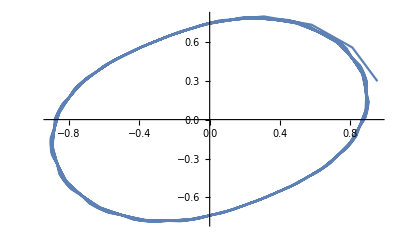

```mathematica
ListPlot[MyList,Joined->True]
```

```mathematica
RRR
```

{(κ λ (1+μ)^2)/(1+κ μ)^2,(κ+μ)^2/(1+κ μ)^2}

```mathematica
RRR/.κ->1+ϵ*x/.λ->1+ϵ*y/.μ->3+ϵ^2
```

{((1+x ϵ) (1+y ϵ) (4+ϵ^2)^2)/((1+(1+x ϵ) (3+ϵ^2))^2),((4+x ϵ+ϵ^2)^2)/((1+(1+x ϵ) (3+ϵ^2))^2)}

```mathematica
Series[{%[[1]]-1,%[[2]]-1},{ϵ,0,3}]
```

{(-x/2+y) ϵ+((3 x^2)/16-(x y)/2) ϵ^2+(-x/8+(3 x^2 y)/16) ϵ^3+O[ϵ]^4,-x ϵ+x^2 ϵ^2+(-x/4-(15 x^3)/16) ϵ^3+O[ϵ]^4}

```mathematica
Normal[%/ϵ]
```

{-x/2+y+((3 x^2)/16-(x y)/2) ϵ+(-x/8+(3 x^2 y)/16) ϵ^2,-x+x^2 ϵ+(-x/4-(15 x^3)/16) ϵ^2}

```mathematica
xy=%
```

{-x/2+y+((3 x^2)/16-(x y)/2) ϵ+(-x/8+(3 x^2 y)/16) ϵ^2,-x+x^2 ϵ+(-x/4-(15 x^3)/16) ϵ^2}

```mathematica
J=D[xy/.ϵ->0,{{x,y},1}]
```

{{-1/2,1},{-1,0}}

```mathematica
Inverse[{{a11,a12},{a21,a22}}].J.{{a11,a12},{a21,a22}}=={{1/4 (-1+ⅈ √15),0},{0,1/4 (-1-ⅈ √15)}}
```

{{(a21 a22)/(-a12 a21+a11 a22)+a11 (a12/(-a12 a21+a11 a22)-a22/(2 (-a12 a21+a11 a22))),a22^2/(-a12 a21+a11 a22)+a12 (a12/(-a12 a21+a11 a22)-a22/(2 (-a12 a21+a11 a22)))},{-a21^2/(-a12 a21+a11 a22)+a11 (-a11/(-a12 a21+a11 a22)+a21/(2 (-a12 a21+a11 a22))),-(a21 a22)/(-a12 a21+a11 a22)+a12 (-a11/(-a12 a21+a11 a22)+a21/(2 (-a12 a21+a11 a22)))}}=={{1/4 (-1+ⅈ √15),0},{0,1/4 (-1-ⅈ √15)}}

```mathematica
Solve[%,{a11,a12,a21,a22}]
```

{{a21→1/4 (a11+ⅈ √15 a11),a22→1/4 (a12-ⅈ √15 a12)}}

```mathematica
{{a11,a12},{a21,a22}}/.%[[1]]
```

{{a11,a12},{1/4 (a11+ⅈ √15 a11),1/4 (a12-ⅈ √15 a12)}}

```mathematica
Det[%]
```

-1/2 ⅈ √15 a11 a12

```mathematica
Solve[%==1,a12]
```

{{a12→(2 ⅈ)/(√15 a11)}}

```mathematica
Ort=%%%/.%[[1]]
```

{{a11,(2 ⅈ)/(√15 a11)},{1/4 (a11+ⅈ √15 a11),1/4 (2/a11+(2 ⅈ)/(√15 a11))}}

```mathematica
Ort=Simplify[%]
```

{{a11,(2 ⅈ)/(√15 a11)},{1/4 (a11+ⅈ √15 a11),(15+ⅈ √15)/(30 a11)}}

```mathematica
Det[Ort]
```

1

```mathematica
Inverse[Ort].Ort
```

{{1/30 (15+ⅈ √15)-(ⅈ (a11+ⅈ √15 a11))/(2 √15 a11),0},{1/4 a11 (-a11-ⅈ √15 a11)+1/4 a11 (a11+ⅈ √15 a11),1/30 (15+ⅈ √15)+(ⅈ (-a11-ⅈ √15 a11))/(2 √15 a11)}}

```mathematica
Simplify[%]
```

{{1,0},{0,1}}

```mathematica
Simplify[Inverse[Ort].J.Ort]
```

{{1/4 ⅈ (ⅈ+√15),0},{0,-1/4 ⅈ (-ⅈ+√15)}}

```mathematica
Simplify[%]
```

{{1,0},{0,1}}

```mathematica
Simplify[Ort/.a11->1]
```

{{1,(2 ⅈ)/(√15)},{1/4 (1+ⅈ √15),1/2+ⅈ/(2 √15)}}

```mathematica
Ort.{u,v}
```

{a11 u+(2 ⅈ v)/(√15 a11),1/4 (a11+ⅈ √15 a11) u+((15+ⅈ √15) v)/(30 a11)}

```mathematica
xy/.x->%[[1]]/.y->%[[2]]
```

{1/4 (a11+ⅈ √15 a11) u+((15+ⅈ √15) v)/(30 a11)+1/2 (-a11 u-(2 ⅈ v)/(√15 a11))+(3/16 (a11 u+(2 ⅈ v)/(√15 a11))^2-1/2 (a11 u+(2 ⅈ v)/(√15 a11)) (1/4 (a11+ⅈ √15 a11) u+((15+ⅈ √15) v)/(30 a11))) ϵ+(1/8 (-a11 u-(2 ⅈ v)/(√15 a11))+3/16 (a11 u+(2 ⅈ v)/(√15 a11))^2 (1/4 (a11+ⅈ √15 a11) u+((15+ⅈ √15) v)/(30 a11))) ϵ^2,-a11 u-(2 ⅈ v)/(√15 a11)+(a11 u+(2 ⅈ v)/(√15 a11))^2 ϵ+(1/4 (-a11 u-(2 ⅈ v)/(√15 a11))-15/16 (a11 u+(2 ⅈ v)/(√15 a11))^3) ϵ^2}

```mathematica
Simplify[Inverse[Ort].%]
```

{1/(2400 a11^4)(15 (15-31 ⅈ √15) a11^5 u^2 ϵ+20 (63+ⅈ √15) a11^3 u v ϵ+4 (5+11 ⅈ √15) a11 v^2 ϵ+360 ⅈ √15 a11^6 u^3 ϵ^2+4 (33-ⅈ √15) v^3 ϵ^2-4 ⅈ a11^2 v (5 (-7 ⅈ+√15)+3 (-5 ⅈ+19 √15) u v) ϵ^2+5 ⅈ a11^4 u (120 (ⅈ+√15)+(30 ⅈ+14 √15+3 (129 ⅈ+√15) u v) ϵ^2)),1/(9600 a11^2)(150 (33+ⅈ √15) a11^5 u^2 ϵ+120 (5+21 ⅈ √15) a11^3 u v ϵ+120 ⅈ (31 ⅈ+√15) a11 v^2 ϵ-225 ⅈ (-33 ⅈ+√15) a11^6 u^3 ϵ^2+384 ⅈ √15 v^3 ϵ^2+60 a11^4 u (5 ⅈ (7 ⅈ+√15)+3 (5-19 ⅈ √15) u v) ϵ^2+20 a11^2 v (-120 ⅈ (-ⅈ+√15)+(-30-14 ⅈ √15+387 u v+3 ⅈ √15 u v) ϵ^2))}

```mathematica
Collect[%,ϵ,Factor]
```

{1/4 ⅈ (ⅈ+√15) u+((225 a11^4 u^2-465 ⅈ √15 a11^4 u^2+1260 a11^2 u v+20 ⅈ √15 a11^2 u v+20 v^2+44 ⅈ √15 v^2) ϵ)/(2400 a11^3)+1/(2400 a11^4)(-150 a11^4 u+70 ⅈ √15 a11^4 u+360 ⅈ √15 a11^6 u^3-140 a11^2 v-20 ⅈ √15 a11^2 v-1935 a11^4 u^2 v+15 ⅈ √15 a11^4 u^2 v-60 a11^2 u v^2-228 ⅈ √15 a11^2 u v^2+132 v^3-4 ⅈ √15 v^3) ϵ^2,-1/4 ⅈ (-ⅈ+√15) v+((165 a11^4 u^2+5 ⅈ √15 a11^4 u^2+20 a11^2 u v+84 ⅈ √15 a11^2 u v-124 v^2+4 ⅈ √15 v^2) ϵ)/(320 a11)+1/(9600 a11^2)(-2100 a11^4 u+300 ⅈ √15 a11^4 u-7425 a11^6 u^3-225 ⅈ √15 a11^6 u^3-600 a11^2 v-280 ⅈ √15 a11^2 v+900 a11^4 u^2 v-3420 ⅈ √15 a11^4 u^2 v+7740 a11^2 u v^2+60 ⅈ √15 a11^2 u v^2+384 ⅈ √15 v^3) ϵ^2}

```mathematica
t1=Coefficient[%,ϵ,1]
```

{(225 a11^4 u^2-465 ⅈ √15 a11^4 u^2+1260 a11^2 u v+20 ⅈ √15 a11^2 u v+20 v^2+44 ⅈ √15 v^2)/(2400 a11^3),(165 a11^4 u^2+5 ⅈ √15 a11^4 u^2+20 a11^2 u v+84 ⅈ √15 a11^2 u v-124 v^2+4 ⅈ √15 v^2)/(320 a11)}

```mathematica
t2=Coefficient[%%%,ϵ,2]
```

{1/(2400 a11^4)(-150 a11^4 u+70 ⅈ √15 a11^4 u+360 ⅈ √15 a11^6 u^3-140 a11^2 v-20 ⅈ √15 a11^2 v-1935 a11^4 u^2 v+15 ⅈ √15 a11^4 u^2 v-60 a11^2 u v^2-228 ⅈ √15 a11^2 u v^2+132 v^3-4 ⅈ √15 v^3),1/(9600 a11^2)(-2100 a11^4 u+300 ⅈ √15 a11^4 u-7425 a11^6 u^3-225 ⅈ √15 a11^6 u^3-600 a11^2 v-280 ⅈ √15 a11^2 v+900 a11^4 u^2 v-3420 ⅈ √15 a11^4 u^2 v+7740 a11^2 u v^2+60 ⅈ √15 a11^2 u v^2+384 ⅈ √15 v^3)}

```mathematica
Series[t2/.u->q*u/.v->q*v,{q,0,1}]
```

{(-u/16+(7 ⅈ u)/(16 √15)-(7 v)/(120 a11^2)-(ⅈ v)/(8 √15 a11^2)) q+O[q]^2,1/480 ⅈ (105 ⅈ a11^2 u+15 √15 a11^2 u+30 ⅈ v-14 √15 v) q+O[q]^2}

```mathematica
t2=Normal[%/q]
```

{-u/16+(7 ⅈ u)/(16 √15)-(7 v)/(120 a11^2)-(ⅈ v)/(8 √15 a11^2),1/480 ⅈ (105 ⅈ a11^2 u+15 √15 a11^2 u+30 ⅈ v-14 √15 v)}

```mathematica
Solve[t1==ϵ*t2,{u,v}]
```

{{v→(15 (7 ⅈ a11^2 u+2 √15 a11^2 u))/(2 (-30 ⅈ+7 √15))},{u→-(ⅈ (-30 ⅈ ϵ+7 √15 ϵ))/(240 a11),v→1/32 (7 a11 ϵ-2 ⅈ √15 a11 ϵ)},{u→-(ⅈ (-30 ⅈ ϵ+7 √15 ϵ))/(240 a11),v→1/32 (7 a11 ϵ+2 ⅈ √15 a11 ϵ)}}

```mathematica
Factor[%]
```

{{v→(15 (7 ⅈ+2 √15) a11^2 u)/(2 (-30 ⅈ+7 √15))},{u→-(ⅈ (-30 ⅈ+7 √15) ϵ)/(240 a11),v→1/32 (7-2 ⅈ √15) a11 ϵ},{u→-(ⅈ (-30 ⅈ+7 √15) ϵ)/(240 a11),v→1/32 (7+2 ⅈ √15) a11 ϵ}}

```mathematica
Simplify[%/.a11->1/(7+2 ⅈ √15)]
```

{{v→(15 (7 ⅈ+2 √15) u)/(218 (30 ⅈ+7 √15))},{u→-(109 ⅈ ϵ)/(16 √15),v→((7-2 ⅈ √15) ϵ)/(32 (7+2 ⅈ √15))},{u→-(109 ⅈ ϵ)/(16 √15),v→ϵ/32}}